```mathematica
Needs["VariationalMethods`"];
ClearAll["Global`*"];
pars = {Subscript[m, b]->0.450,Subscript[m, p]->0.5,r->0.25, l->0.23, g->9.81};
T[t_]=1/2 Subscript[m, b] x'[t]^2 + 1/2(2/3 Subscript[m, b])x'[t]^2+1/2 Subscript[m, p](l θ'[t] Cos[θ[t]]+x'[t])^2+1/2 Subscript[m, p](l θ'[t] Sin[θ[t]])^2;
V[t_]=- Subscript[m, p]g l Cos[θ[t]];
L[t_]= T[t] - V[t]
(*eqns = {EulerEquations[L[t],x[t],t]/.{0->(-F[t])/r},EulerEquations[L[t],θ[t],t]/.{0->-F[t]}}*)
eqns={D[D[L[t],x'[t]],t] - D[L[t],x[t]] == F[t]/r,Simplify[D[D[L[t],θ'[t]],t] - D[L[t],θ[t]]]==-F[t]}
bb8 = NonlinearStateSpaceModel[eqns, {{x[t],4},{θ[t],0°}},{F[t]},{x[t],θ[t]},t]
bb8linear  = StateSpaceModel[bb8]
(*ToDiscreteTimeModel[bb8linear,0.01, Method->"ZeroOrderHold"];*)
k = LQRegulatorGains[StateSpaceModel[bb8/.pars],{IdentityMatrix[4],{{1}}}]
bb8lin = SystemsModelStateFeedbackConnect[bb8,k]
```

g l Cos[θ[t]] m_p+5/6 m_b x'[t]^2+1/2 l^2 Sin[θ[t]]^2 m_p θ'[t]^2+1/2 m_p (x'[t]+l Cos[θ[t]] θ'[t])^2

{5/3 m_b x''[t]+m_p (-l Sin[θ[t]] θ'[t]^2+x''[t]+l Cos[θ[t]] θ''[t])==F[t]/r,l m_p (g Sin[θ[t]]+Cos[θ[t]] x''[t]+l θ''[t])==-F[t]}

x_2[t](l Cos[x_3[t]] m_p (-F[t]-g l Sin[x_3[t]] m_p))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)-(l^2 m_p (F[t]/r+l Sin[x_3[t]] m_p x_4[t]^2))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)x_4[t]((-(5 m_b)/3-m_p) (-F[t]-g l Sin[x_3[t]] m_p))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)+(l Cos[x_3[t]] m_p (F[t]/r+l Sin[x_3[t]] m_p x_4[t]^2))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)x_1[t]x_3[t]{x_1[t],4}x_2[t]{x_3[t],0}x_4[t] 4122NoneNoneFalseFalseFalse{F[t]}t

0100000(3 g m_p)/(5 m_b)03/(5 l m_b)+3/(5 r m_b)0001000(3 g (-(5 m_b)/3-m_p))/(5 l m_b)0-3/(5 l r m_b)+(3 (-(5 m_b)/3-m_p))/(5 l^2 m_b m_p)1000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNone,{{x_1[t],0},{x_2[t],0},{x_3[t],0},{x_4[t],0}},{{F[t],0}},Automatic,t

{{1.,1.85064,-2.37488,-0.797751}}

x_2[t](l Cos[x_3[t]] m_p (-g l Sin[x_3[t]] m_p-u_1[t]+1. (-4+x_1[t])+1.85064 x_2[t]-2.37488 x_3[t]-0.797751 x_4[t]))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)-(l^2 m_p ((u_1[t]-1. (-4+x_1[t])-1.85064 x_2[t]+2.37488 x_3[t]+0.797751 x_4[t])/r+l Sin[x_3[t]] m_p x_4[t]^2))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)x_4[t]((-(5 m_b)/3-m_p) (-g l Sin[x_3[t]] m_p-u_1[t]+1. (-4+x_1[t])+1.85064 x_2[t]-2.37488 x_3[t]-0.797751 x_4[t]))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)+(l Cos[x_3[t]] m_p ((u_1[t]-1. (-4+x_1[t])-1.85064 x_2[t]+2.37488 x_3[t]+0.797751 x_4[t])/r+l Sin[x_3[t]] m_p x_4[t]^2))/(-5/3 l^2 m_b m_p-l^2 m_p^2+l^2 Cos[x_3[t]]^2 m_p^2)x_1[t]x_3[t]{x_1[t],4}x_2[t]{x_3[t],0}x_4[t] 4122NoneNoneFalseFalseFalse{u_1[t]}t

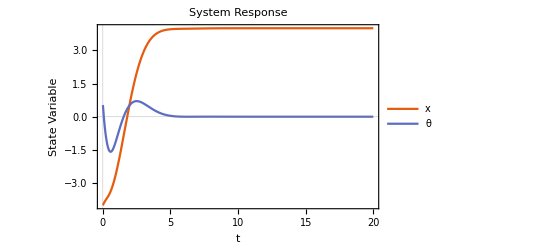

```mathematica
resp=OutputResponse[{bb8lin/.pars, {-4, 0.3, 30°,0}}, 0, {t, 0, 20}];
xs[t_]=resp[[1]];
θs[t_]=resp[[2]];
Plot[{xs[t],θs[t]}, {t, 0, 20}, PlotLegends->{"x","θ"}, PlotLabel->"System Response", AxesLabel->{"t","State Variable"}, PlotTheme->"Scientific"]
Animate[Graphics[{Green, Disk[{xs[t],r},r], Yellow, Line[{{xs[t]-r Sin[xs[t]/r],r-r Cos[xs[t]/r]},{xs[t]+r Sin[xs[t]/r],r+r Cos[xs[t]/r]}}], Black,Line[{{xs[t],r},{xs[t]+l Sin[θs[t]],r-l Cos[θs[t]]}}], Disk[{xs[t]+l Sin[θs[t]],r-l Cos[θs[t]]}, 0.2l],Blue, BezierCurve[Table[{xs[n]+l Sin[θs[n]],r-l Cos[θs[n]]},{n,0,t,0.01}]],Orange, BezierCurve[Table[{xs[n],r},{n,0,t,0.01}]]}, PlotRange->{{-6,6},{0,1}},GridLines->Automatic]/.pars,{t,0,20}, AnimationRunning->False]
(*Export["dpend_sim2.gif",Table[Graphics[{Green, Disk[{xs[t],r},r], Yellow, Line[{{xs[t]-r Sin[xs[t]/r],r-r Cos[xs[t]/r]},{xs[t]+r Sin[xs[t]/r],r+r Cos[xs[t]/r]}}], Black,Line[{{xs[t],r},{xs[t]+l Sin[θs[t]],r-l Cos[θs[t]]}}], Disk[{xs[t]+l Sin[θs[t]],r-l Cos[θs[t]]}, 0.1],Blue, BezierCurve[Table[{xs[n]+l Sin[θs[n]],r-l Cos[θs[n]]},{n,0,t,0.01}]],Orange, BezierCurve[Table[{xs[n],r},{n,0,t,0.01}]]}, PlotRange->{{-6,6},{0,3}},Background->Lighter[Gray, 0.8], ImageSize->1000]/.pars,{t,0,15,0.083333}],"FrameRate"->24]*)
```

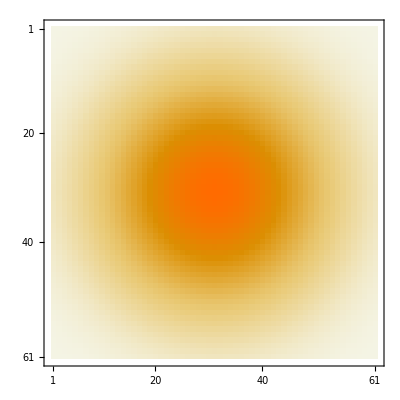

```mathematica
MatrixPlot[Table[1/(2π)^0.5 ⅇ^(-(i^2+j^2)/2),{i,-3,3,0.1},{j,-3,3,0.1}]]
```